0

1

0.5+0.87 ⅈ

0.5+0.87 ⅈ

1/3

2/3

0.501142-0.288013 ⅈ

{0,1/3,0.501142-0.288013 ⅈ,2/3,1,0.5+0.87 ⅈ,0}

{{0,0},{1/3,0},{0.501142,-0.288013},{2/3,0},{1,0},{0.5,0.87},{0,0}}

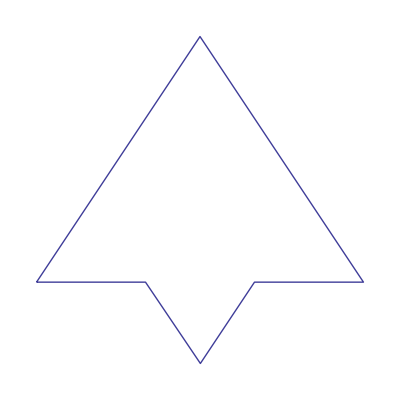

{}

```mathematica
a=0
b=1
c=0.5+0.87I
cons=0.5+0.87I
d=(2a+b)/3
e=(a+2b)/3
f=(-(e*c)+d)/(1-c)
L={a,d,f,e,b,c,a}
g[z_]:={Re[z],Im[z]}
Q=Map[g,L]
ListPlot[{Q},AspectRatio->1,Joined->True,Axes->None]
G={}
```

```mathematica
{{0,0},{1/3,0},{0.5011421193763035,-0.2880127122852319},{2/3,0},{1,0},{0.5,0.87}}
```

{{0,0},{1/3,0},{0.501142,-0.288013},{2/3,0},{1,0},{0.5,0.87}}

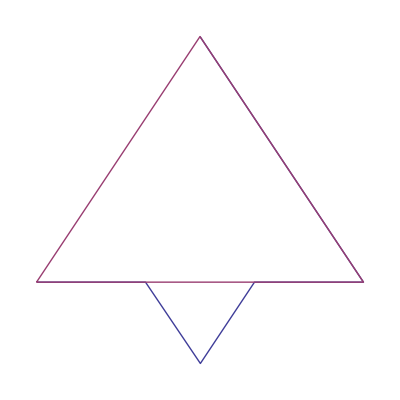

```mathematica
L={0,1,0.5+0.87I,0}
```

{0,1,0.5+0.87 ⅈ,0}

```mathematica
L=M;
```

```mathematica
M={}
```

{}

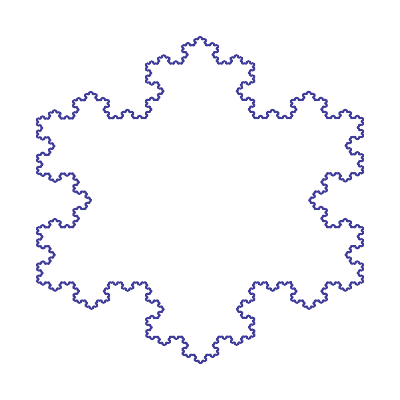

```mathematica
Do[M1={L[[k]],(2*L[[k]]+L[[k+1]])/3,
(-((L[[k]]+2*L[[k+1]])/3*cons)+(2*L[[k]]+L[[k+1]])/3)/(1-cons),
(L[[k]]+2*L[[k+1]])/3,L[[k+1]]};M=Join[M,M1],
{k,1,Length[L]-1}];
g[z_]:={Re[z],Im[z]};
Q=Map[g,M];
ListPlot[{Q},AspectRatio->1,Joined->True,Axes->None]
```

```mathematica
M={}
```

{}

```mathematica
M
```

{0.334478-0.192666 ⅈ,0.371387-0.192447 ⅈ,0.390158-0.224228 ⅈ,0.408297-0.192228 ⅈ,0.445206-0.192008 ⅈ}

```mathematica
Flocon[p_]:=Module[{t=p,m=1},
While[m≤p,
Do[M1={L[[k]],(2*M[[k]]+L[[k+1]])/3,(-((L[[k]]+2*L[[k+1]])/3*cons)+(2*L[[k]]+L[[k+1]])/3)/(1-cons),(L[[k]]+2*L[[k+1]])/3,L[[k+1]]},{k,1,Length[L]-1}];
Join[M,M1];m=m+1];
g[z_]:={Re[z],Im[z]};
Q=Map[g,M];
ListPlot[{Q},AspectRatio->Automatic,Joined->True,Axes->None]]
```

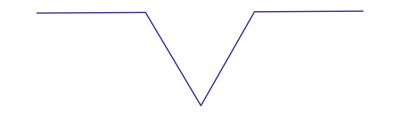

```mathematica
Flocon[1]
```